```mathematica
SetDirectory[NotebookDirectory[]];
Off[NDSolve::"ndsz"]
Off[NDSolve::maxit]
Off[NDSolve::"noout"]
$PlotTheme=None;(* plots in Mathematica10 looks like in previous versions *)
```

Charged particle trajectory in magnetic field around black hole is calculated using Hamiltonian formalism -  more information can be found in: 
M Kološ, Z Stuchlík, A Tursunov: Quasi-harmonic oscillatory motion of charged particles around a Schwarzschild black hole immersed in a uniform magnetic field, Classical and Quantum Gravity 32 (16), 165009

## GiveMeTrajectory

```mathematica
Clear[RH,draha,begin,end,R0,θ0,B,J,Q,text,param,k,kk,LL,EE]

Clear[M,B,k,gtt,gtϕ,gϕϕ,grr,gθθ,gUtt,gUtϕ,gUϕϕ,gUrr,gUθθ,qAt,qAϕ,Veff,amA,amB,amC];

(* 2D - polar coordinates *)
XX[r_,ϕ_]:=r Cos[ϕ];YY[r_,ϕ_]:=r Sin[ϕ];

(* 3D - spherical coordinates *)
XXX[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ];
YYY[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ];
ZZZ[r_,θ_,ϕ_]:=r Cos[θ];

(*---- Metrics coefficients ----*)
AA[r_]:=(1-(2M)/r);
(* lower indicies *)
 gtt[r_,θ_]:=-AA[r];grr[r_,θ_]:=1/AA[r];gθθ[r_,θ_]:= r^2;gϕϕ[r_,θ_]:=r^2 Sin[θ]^2;
(* upper indicies *)
gUtt[r_,θ_]:=1/gtt[r,θ];gUrr[r_,θ_]:=1/grr[r,θ];gUθθ[r_,θ_]:= 1/gθθ[r,θ];gUϕϕ[r_,θ_]:=1/gϕϕ[r,θ]; 
(*---- Metrics coefficients ----*)

(*---- Effective potential ----*)
(* ! sf. sym. metric only ! *)
(* H==0 & pr==0 & pθ==0 => 1/2( gUtt[r,θ](EE+qAt[r,θ])^2+gUϕϕ[r,θ](LL-qAϕ[r,θ])^2)+1/2 == 0 | (EE-qAt[r,θ])^2==-gtt[r,θ](gUϕϕ[r,θ](LL-qAϕ[r,θ])^2 +1) *)
Veff[r_,θ_,L_]:=qAt[r,θ]+√(-gtt[r,θ](1+gUϕϕ[r,θ] (L-qAϕ[r,θ])^2));
(*---- Effective potential ----*)


GiveMeTrajectory[R0_,θ0_,LL_,xEND_]:=((* particle trajectory is calculated, Hamilton formalism for chrged particle motion is used *)
Clear[r,pr,θ, pθ,ϕ,EE];

EE=Veff[R0,θ0,LL];

Hamiltonian[r_,θ_,pr_,pθ_]:=1/2 gUrr[r,θ] pr^2+1/2 gUθθ[r,θ] pθ^2+1/2( gUtt[r,θ](EE+qAt[r,θ])^2+gUϕϕ[r,θ](LL-qAϕ[r,θ])^2)+1/2;
(* pr = Subscript[p, r], qAt = Subscript[qA, t] - lower index *) (* r = x^r, gUrr = g^rr - upper index *)
DrHamiltonian[r_,θ_,pr_,pθ_]:=D[Hamiltonian[r,θ,pr,pθ], r];DθHamiltonian[r_,θ_,pr_,pθ_]:=D[Hamiltonian[r,θ,pr,pθ], θ];

Equations ={
r'[τ]   ==    gUrr[r[τ] ,θ[τ]]pr[τ],
pr'[τ]  == -DrHamiltonian[r[τ],θ[τ],pr[τ],pθ[τ]],
θ'[τ]   ==   gUθθ[r[τ] ,θ[τ] ]pθ[τ],
pθ'[τ]  ==-DθHamiltonian[r[τ],θ[τ],pr[τ],pθ[τ]],
ϕ'[τ]   ==    gUϕϕ[r[τ] ,θ[τ]]LL-gUϕϕ[r[τ] ,θ[τ]]qAϕ[r[τ],θ[τ]]  
(* ϕ' = p^ϕ = g^ϕϕ Subscript[p, ϕ] = g^ϕϕ L - g^ϕϕ Subscript[qA, ϕ] *) 
(* t' = we do not need to calculate, becouse the model is nedependent of t and ϕ (stacionarity, axill symmetry) and t coordinate is not used for plots (as ϕ does) *)
};
IntCond ={r[0]    == R0, pr[0]   ==  0,θ[0]   == θ0, pθ[0]  == 0,ϕ[0]   == 0};

(*---- Hamiltonian a equations of motion ----*)

(*---- trajectory calculation ----*)
HamI=Hamiltonian[r[τ],θ[τ],pr[τ],pθ[τ]];
stepsize=10^-1;(*Metoda=Automatic;*)
(* put your favourite numerical method here *)
Metoda={"StiffnessSwitching", Method->{ {"Projection", Method->{"ExplicitRungeKutta","DifferenceOrder"->8},"Invariants"->HamI},Automatic}};
(* put your favourite numerical method here *)

draha=NDSolve[{Equations,IntCond},{r,pr,θ,pθ,ϕ},{τ,0,xEND},{Method->{"EventLocator","Event"->{r[τ]-Rend,r[τ]-xInfinity},"EventAction":>{Throw[ Null,"StopIntegration"],Throw[Null, "StopIntegration"]},"Method"->Metoda},{StartingStepSize->10^-1,MaxSteps->∞}}];
ipub=r/.draha[[1,1]];domain=ipub["Domain"];{begin,end} = domain[[1]];
(*---- trajectory calculation ----*)

text=Row[{"Hamiltonian, k=0"}];

);

ShowTrajectory[colour_]:=(
(* this function will show particle trajectory
colour = particle trajectory colour; 
black dashed = boundary for the particle motion, AKA energy boundary fuction AKA curve of zero velocity;
gray curves = magnetic field lines *)
GraphicsRow[{pic1=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->oblast2D,Epilog->{PointSize[0.02],Point[{XXX[R0,θ0,0],YYY[R0,θ0,0]}],LightGray,Disk[{0,0},RH]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz],
pic2=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]],ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->oblast2D,Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,
Epilog->{PointSize[0.02],Point[{XXX[R0,θ0,0],ZZZ[R0,θ0,0]}],
Text[Row[{cl,"≐",Round[LL,0.01],", ",ce,"≐",Round[EE,0.01]}],Scaled[{0.5,0.9}]],
Text[Row[{"r_0≐",Round[R0,0.1],", θ_0≐",Round[Pi/2,0.1]}],Scaled[{0.5,0.1}]]
}],
pic3=Show[
ParametricPlot[ {XXX[r[τ],θ[τ],0],ZZZ[r[τ],θ[τ],0] }/.draha,{τ,begin, end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->{{0,oblast1D[[2]]},{oblast1D[[1]]/2,oblast1D[[2]]/2}},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,Epilog->{LightGray,Disk[{0,0},RH],Black,PointSize[0.02],Point[{XXX[R0,θ0,0],ZZZ[R0,θ0,0]}]}],
ContourPlot[ Abs[qAϕ[√(xx^2+zz^2),ArcTan[xx/zz]]],{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourShading->None,ContourStyle->{Gray}],
ContourPlot[Veff[√(xx^2+zz^2),ArcTan[xx/zz],LL]==EE,{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourStyle->{{Black,Thick,Dashed}}]
],
pic4=Show[ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotRange->oblast3D,BoxStyle->{Black},PlotStyle->{colour},ViewPoint->{0,-3,1},Ticks->None,ImageSize->ImSz],
Graphics3D[{{Black,Text[Style[param,fontyW],{0,0,-10}]},{LightGray,Sphere[{0,0,0},RH]},{Black,PointSize[0.02],Point[{XXX[R0,θ0,0],YYY[R0,θ0,0],ZZZ[R0,θ0,0]}]}}],Lighting->"Neutral"]
}]
);

fonty=15;fontyW={FontSize->15,Background->White};ImSz=250;ce="ℰ";cl="ℒ";cb="ℬ";

oblast1D={-11,11};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};

M=1;RH=2;Rend =1.001RH;xInfinity=1000;
```

```mathematica
param="geodesic";qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=0;
R0=7;θ0=Pi/2+0.3;LL=3.3;konec=400;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
param="geodesic";qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=0;
R0=7;θ0=Pi/2+0.3;LL=3.34;konec=400;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

## Uniform magnetic field

```mathematica
B=0.1;param=Row[{"uniform | ",cb,"=",B}];qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=B gϕϕ[r,θ];
R0=7;θ0=Pi/2+0.1;LL=7;konec=400;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
B=-1;param=Row[{"uniform | ",cb,"=",B}];qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=B gϕϕ[r,θ];
R0=4;θ0=Pi/2+0.3;LL=63;konec=50;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

## Split monopole magnetic field

```mathematica
(* √(Cos[θ]^2) =  RealAbs[ Cos[θ] ] = absolut value of Cos function *)
```

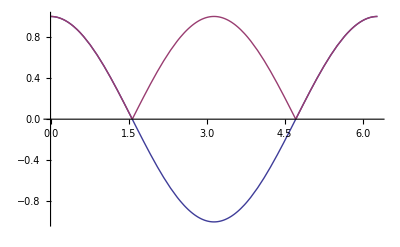

```mathematica
Plot[{Cos[θ],√(Cos[θ]^2)},{θ,0,2Pi}]
```

```mathematica
qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=e RealAbs[Cos[θ]];qAϕ[r_,θ_]:=e √(Cos[θ]^2);e=-1;param=Row[{"monopole | e=",e}];
R0=8;θ0=Pi/2-0.2;LL=Sin[θ0]3.5;konec=500;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=e RealAbs[Cos[θ]];qAϕ[r_,θ_]:=e √(Cos[θ]^2);e=-1;param=Row[{"monopole | e=",e}];
R0=7;θ0=Pi/2-0.0001;LL=3.5;konec=500;GiveMeTrajectory[R0,θ0,LL,konec];pic=ShowTrajectory[Blue]
```

-Graphics-

```mathematica
qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=e RealAbs[Cos[θ]];qAϕ[r_,θ_]:=e √(Cos[θ]^2);e=1;param=Row[{"monopole | e=",e}];
R0=7;θ0=Pi/2-0.0001;LL=3.5;konec=600;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=e RealAbs[Cos[θ]];qAϕ[r_,θ_]:=e √(Cos[θ]^2);
e=1;param=Row[{"monopole | e=",e}];
R0=7;θ0=1.2;LL=3.7;konec=500;
GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=e RealAbs[Cos[θ]];qAϕ[r_,θ_]:=e √(Cos[θ]^2);e=-1;param=Row[{"monopole | e=",e}];
R0=7;θ0=1.2;LL=3;konec=500;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=e  √(Cos[θ]^2);
e=1;param=Row[{"monopole | e=",e}];

LL=3.7;
R0=1/2 (-e^2+LL^2+√(12 e^2+e^4-12 LL^2-2 e^2 LL^2+LL^4));θ0=ArcTan[(√(LL^2-e^2))/e]-0.000001;
N[{R0,θ0}]

konec=500;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

{7.82454,1.29712}

-Graphics-

## Parabolic field

```mathematica
kk=0.1;RG=2;param=Row[{"parabolic | ",k,"=",kk}];
Phi[r_,θ_]:=kk(r(1-RealAbs[Cos[θ]])+RG( 1+RealAbs[Cos[θ]])(1-Log[1+RealAbs[Cos[θ]]])-2RG(1-Log[2]));qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
R0=7;θ0=1;LL=3;konec=100;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
kk=2;RG=2;param=Row[{"parabolic | ",k,"=",kk}];
Phi[r_,θ_]:=kk(r(1-RealAbs[Cos[θ]])+RG( 1+RealAbs[Cos[θ]])(1-Log[1+RealAbs[Cos[θ]]])-2RG(1-Log[2]));qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
R0=8;θ0=1.2;LL=10;konec=100;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
kk=2;RG=2;param=Row[{"parabolic | ",k,"=",kk}];
Phi[r_,θ_]:=kk(r(1-RealAbs[Cos[θ]])+RG( 1+RealAbs[Cos[θ]])(1-Log[1+RealAbs[Cos[θ]]])-2RG(1-Log[2]));qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
R0=8;θ0=1.2;LL=11;konec=100;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
kk=-2;RG=2;param=Row[{"parabolic | ",k,"=",kk}];
Phi[r_,θ_]:=kk(r(1-RealAbs[Cos[θ]])+RG( 1+RealAbs[Cos[θ]])(1-Log[1+RealAbs[Cos[θ]]])-2RG(1-Log[2]));qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
R0=5;θ0=1.5;LL=2;konec=100;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
kk=-0.5;RG=2;param=Row[{"parabolic | ",k,"=",kk}];
Phi[r_,θ_]:=kk(r(1-RealAbs[Cos[θ]])+RG( 1+RealAbs[Cos[θ]])(1-Log[1+RealAbs[Cos[θ]]])-2RG(1-Log[2]));qAt[r_,θ_]:=0; qAϕ[r_,θ_]:=Phi[r,θ];
R0=7;θ0=1;LL=2;konec=100;GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

## Dipole magnetic field

```mathematica
k=-7;param=Row[{"mag. dipole | k=",k}];qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=k r^2 Sin[θ]^2(Log[1-(2M)/r]+(2M)/r(1+M/r));
R0=8;θ0=Pi/2+0.4;LL=7;konec=100;
GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

## Beskin disk

```mathematica
k=10;b=6;param=Row[{"Beskin disk (flat) | k=",k}];

qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=k(1-√(1/2(1-r^2/b^2)+√(1/4(1-r^2/b^2)^2+r^2/b^2 Cos[θ]^2)));
```

```mathematica
R0=4;θ0=Pi/2+0.3;LL=5;konec=300;
GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
R0=4;θ0=Pi/2+0.3;LL=7;konec=30;
GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

## Petterson loop

```mathematica
Clear[a];
fceK2[r_,θ_,a_]:=(4 a r Sin[θ])/(a^2+r^2+2a r Sin[θ]);qAt[r_,θ_]:=0;qAϕ[r_,θ_]:=k(4 a r Sin[θ])/(√(a^2+r^2+2a r Sin[θ]))(((2-fceK2[r,θ,a])EllipticK[fceK2[r,θ,a]]-2EllipticE[fceK2[r,θ,a]])/fceK2[r,θ,a]);
k=1;a=6;param=Row[{"Petterson loop (flat) | k=",k}];
```

```mathematica
R0=4;θ0=Pi/2+0.3;LL=10;konec=50;
GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
R0=4;θ0=Pi/2+0.3;LL=12;konec=100;
GiveMeTrajectory[R0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-